```mathematica
p[x_]:=2*Sqrt[2]/3/Pi^2*NIntegrate[z^(3/2)/(Exp[z-x]+1),{z,0,200}]
```

```mathematica
n[x_]:=Sqrt[2]/Pi^2*NIntegrate[z^(1/2)/(Exp[z-x]+1),{z,0,200}]
```

```mathematica
n[1]
```

0.200086

NIntegrate::inumr: The integrand z^3/2/1 + ⅇ^-x + z has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 200}}.

NIntegrate::inumr: The integrand √z/1 + ⅇ^-x + z has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 200}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

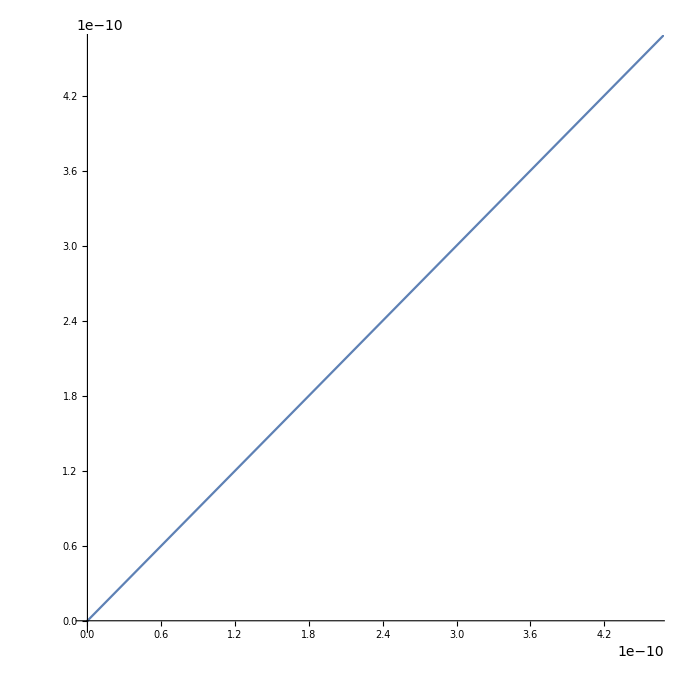

```mathematica
ParametricPlot[{p[x],n[x]},{x,-100,0}]
```

```mathematica
n[0]
```

0.0971639

```mathematica
p[0]
```

```mathematica
0.11012334807030655
```

```mathematica
p[x_]:=Sqrt[2]/3/Pi^2*NIntegrate[z^(3/2)/(Exp[z-x]-1),{z,0,300}]
n[x_]:=1/Sqrt[2]/Pi^2*NIntegrate[z^(1/2)/(Exp[z-x]-1),{z,0,300}]
```

NIntegrate::inumr: The integrand z^3/2/-1 + ⅇ^-x + z has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 300}}.

NIntegrate::inumr: The integrand √z/-1 + ⅇ^-x + z has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 300}}.

NIntegrate::inumr: The integrand z^3/2/-1 + ⅇ^-x + z has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 300}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

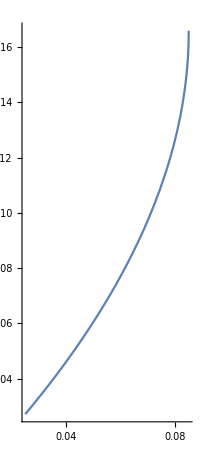

```mathematica
ParametricPlot[{p[x],n[x]},{x,-1,0}]
```

```mathematica
p[0]
```

0.0851759